```mathematica
(*Coment*)
```

Text cell

Creating functions with :=

```mathematica
f[x_] := x^2 + 1
```

```mathematica
f[0]
```

1

```mathematica
f[2]
```

5

5

lists

```mathematica
g={1,2,3}
```

{1,2,3}

Accessing list elements

```mathematica
g{2}
```

Thread::tdlen: Objects of unequal length in {1,2,3} {2} cannot be combined.

```mathematica
{{□}, {}}
```

{2} {1,2,3}

```mathematica
% 99 (*access yo lsdy *)
```

{2} {1,2,3}

```mathematica
3+2
```

5

```mathematica
β
```

β

## Defining functions

```mathematica
f[x_] := Sin[x]
```

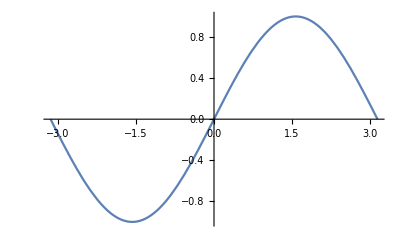

```mathematica
Plot[f[x], {x, -Pi, Pi}]
```

# Lists

```mathematica
A = {1,2,3,4};
```

```mathematica
A[[2]]
```

2

```mathematica
Teste = Table[RandomReal[{0,1}],{i,1,5}]Table[RandomReal[{0,1}],{i,1,5}]
```

{0.55452,0.0706441,0.113156,0.291925,0.0805673}

```mathematica
First[Teste] (*return first item from list*)
```

0.55452

```mathematica
Last[Teste]
```

0.0805673

```mathematica
Total[Teste] (*Sum of everything*)
```

1.11081

```mathematica
Sum[Teste[[i]], {i, 1, 3}] (*partial sum*)
```

0.73832

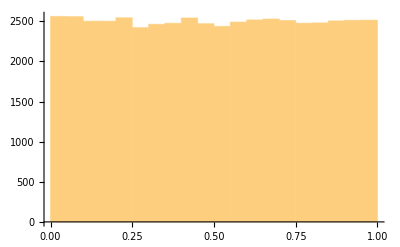

```mathematica
mylist3=Table[RandomReal[],{50000}];
Histogram[mylist3]
```

```mathematica
mymatrix={{1,2.,A,B},{2,4,6,"mytext"}}
MatrixForm[mymatrix]
```

{{1,2.,{1,2,3,4},B},{2,4,6,mytext}}

(1 | 2. | {1,2,3,4} | B
2 | 4 | 6 | mytext)

```mathematica
mytext2=5.3;
mytext2[[0]]
```

Real

```mathematica
vec1={vx, vy, vz};
vec2={wx, wy, wz};
Dot[vec1,vec2]  (* OR  vec1 . vec2 *)
Cross[vec1,vec2]
Norm[vec1]
```

vx wx+vy wy+vz wz

{-vz wy+vy wz,vz wx-vx wz,-vy wx+vx wy}

√(Abs[vx]^2+Abs[vy]^2+Abs[vz]^2)

```mathematica
mymatrix2 = {{a, b}, {-b,a}}
```

{{a,b},{-b,a}}

```mathematica
MatrixForm[mymatrix2]
```

(a | b
-b | a)

```mathematica
MatrixForm[Inverse[mymatrix2]]
```

(a/(a^2+b^2) | -b/(a^2+b^2)
b/(a^2+b^2) | a/(a^2+b^2))

```mathematica
Det[mymatrix2]
```

a^2+b^2

```mathematica
Tr[mymatrix2]
```

2 a

```mathematica
λ=Eigenvalues[mymatrix2]
eigvec=Eigenvectors[mymatrix2]
Eigensystem[mymatrix2]
```

{a-ⅈ b,a+ⅈ b}

{{ⅈ,1},{-ⅈ,1}}

{{a-ⅈ b,a+ⅈ b},{{ⅈ,1},{-ⅈ,1}}}

## Plotting

```mathematica
fplot[x_]:=1/(1+Exp[x])

xmin =0;
xmax = 10;
imax = 100;
```

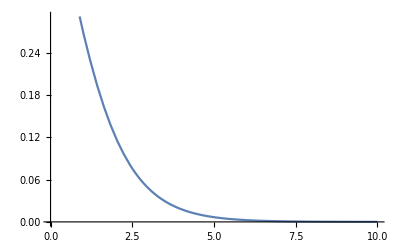

```mathematica
Plot[fplot[x], {x, xmin, xmax}]
```

```mathematica
fList = Table[{1. i xmax/imax, fplot[i xmax/imax]},{i, 1, imax}];
```

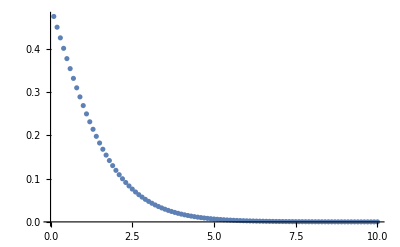

```mathematica
ListPlot[fList]
```